## Mathematica Stock Data

Fundamentals

### Find Stock Quote

```mathematica
FinancialData["DIS"]
```

92.67

### 200-day Average Price

```mathematica
FinancialData["DIS","Average200Day"]
```

97.13

### Currency Exchange Rate

```mathematica
FinancialData["EUR/USD"]
```

1.0971

### Low and High for the Current or Most Recent Trading Day

```mathematica
{FinancialData["DIS","Low"],FinancialData["DIS","High"]}
```

{92.31,93.82}

### Market Cap

```mathematica
FinancialData["DIS","MarketCap"]
```

1.4877×10^11

### # of Shares Available for Trade on Market Open

```mathematica
FinancialData["DIS","FloatShares"]
```

1476443000

### Earnings per Share for the Most Recent Four Quarters

```mathematica
FinancialData["DIS","EarningsPerShare"]
```

5.564

### Price-to-earnings Ratio Based on Trailing Earnings

```mathematica
FinancialData["DIS","PERatio"]
```

16.6415

Estimate of forward PE ratio

```mathematica
FinancialData["DIS","ForwardPERatio"]
```

15.3

### Dividends

Most recent dividend

```mathematica
FinancialData["DIS","Dividend"]
```

0.71

Plot all available dividends

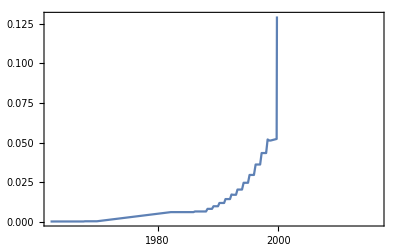

```mathematica
DateListPlot[FinancialData["DIS","Dividend",All]]
```

### Price of Gold

```mathematica
FinancialData["XAU/USD"]
```

1323.

Data for Different Types of Dates

### Multiple Dates

```mathematica
FinancialData["DIS",{{2005,3,10},{2005,3,15}}]
```

```mathematica
{{{2005,3,10},23.575849},{{2005,3,11},23.23063},{{2005,3,14},23.592689},{{2005,3,15},24.081045}}
```

Same calculation; showing only price values

```mathematica
FinancialData["DIS",{{2005,3,10},{2005,3,15}},"Value"]
```

{23.5758,23.2306,23.5927,24.081}

### All Dates

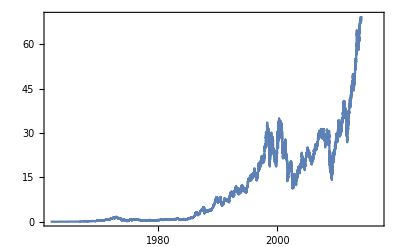

```mathematica
DateListPlot[FinancialData["DIS",All]]
```

Give all available data from a specific date

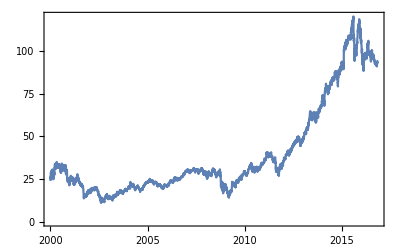

```mathematica
DateListPlot[FinancialData["DIS",{2000,1,1}]]
```

### Specific Date

```mathematica
FinancialData["DIS",{{2005,3,15}}]
```

{{{2005,3,15},24.081}}

Same calculation, give only value

```mathematica
FinancialData["DIS",{{2005,3,15}},"Value"]
```

{24.081}

Trading volume for a day

```mathematica
FinancialData["DIS","Volume",{{2005,3,15}},"Value"]
```

{10866800}

Plots and Charts

### Stock Data for a Time Period

```mathematica
DateListPlot[FinancialData["DIS", "Jan.1,2000"]]
```

-Graphics-

### Two Stocks Together

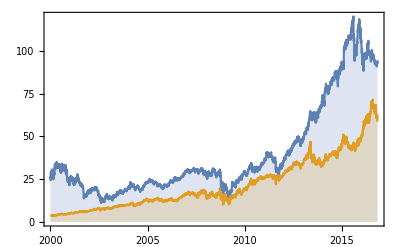

```mathematica
DateListPlot[{FinancialData["DIS",{2000}],FinancialData["O",{2000}]},Joined->True, Filling->Bottom]
```

### Daily Cumulative Fractional Change Since January 1, 2005

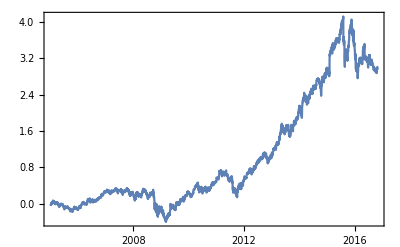

```mathematica
DateListPlot[FinancialData["DIS","CumulativeFractionalChange",{2005,1,1}]]
```

### Plot the Cumulative Changes of a Stock Since 2000 Compared to the S&P 500

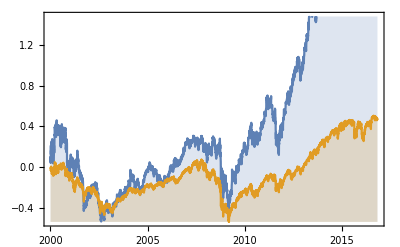

```mathematica
DateListPlot[{FinancialData["DIS","CumulativeFractionalChange", {2000}],FinancialData["SP500","CumulativeFractionalChange", {2000}]},Joined->True, Filling->Bottom]
```

### Find 100-day Moving Averages of a Stock Price

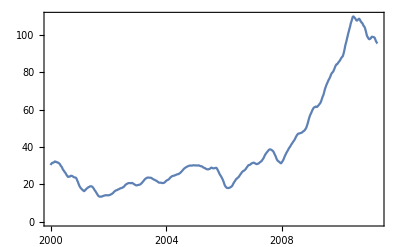

```mathematica
DateListPlot[MovingAverage[FinancialData["DIS","Jan.1,2000","Value"],100],{"Jan.1,2000",Automatic,"Day"}, Joined->True]
```

### Trading Volume

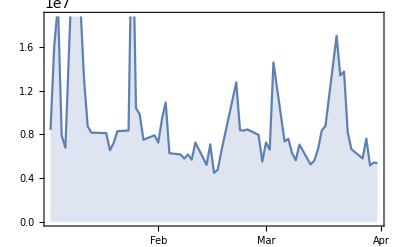

```mathematica
DateListPlot[FinancialData["DIS","Volume",{{2000,1,1}, {2000,4,1}}], Filling->Axis]
```

Computations

### Find the Daily Average Trading Volume for DIS in the First Quarter of 2000

```mathematica
Mean[FinancialData["DIS","Close",{{2000,1,1},{2000,4,1}},"Value"]]
```

28.9155

### Find the Standard Deviation in the Closing Price for DIS in the First Quarter of 2000

```mathematica
StandardDeviation[FinancialData["DIS","Close",{{2000,1,1},{2000,4,1}},"Value"]]
```

2.23275

### Skewness of Price Distribution

```mathematica
Skewness[FinancialData["DIS","Close",{{2000,1,1},{2000,4,1}},"Value"]]
```

0.199231

### Correlation Between Cumulative Returns for Stock and S&P 500

```mathematica
Correlation[FinancialData["DIS","CumulativeReturn",{{2006},{2007}},"Value"],FinancialData["SP500","CumulativeReturn",{{2006},{2007}},"Value"]]
```

0.764543